tests

```mathematica
Get["GeneralFitFunction.m"]
```

```mathematica
ClearAll[TransportIntegration]
```

```mathematica
?TransportIntegration
```

Global`TransportIntegration

TransportIntegration[integrand_[x___],XBinList_List,IntVarList_List,OptionsPattern[]]:=Method[{test=5},{ParallelTable[NIntegrate[integrand[x]/.xi→XBinList⟦xbin⟧,IntVarList,PrecisionGoal→OptionValue[PrecisionGoal],Method→OptionValue[IntMethod]],{xbin,1,Length[XBinList]}],Print[OptionValue[PrecisionGoal],OptionValue[xBinInt]]}]
 
Options[TransportIntegration]={xBinInt→True,PrecisionGoal→3,IntMethod→Automatic}

```mathematica
ClearAll[f]
```

```mathematica
f[x_?NumericQ,xi_?NumericQ]:=x^2+5*xi
```

```mathematica
TransportIntegration[f[x,xi],{1,2,3},{{x,0,1}},xBinInt->False]
```

NIntegrate::ilim: Invalid integration variable or limit(s) in {x,0,1}.

General::stop: Further output of NIntegrate::ilim will be suppressed during this calculation.

3False

{{NIntegrate[f[x,xi]/.xi→{1,2,3}⟦xbin⟧,Sequence@@{{x,0,1}},PrecisionGoal→OptionValue[TransportIntegration,{xBinInt→False},PrecisionGoal],Method→OptionValue[TransportIntegration,{xBinInt→False},IntMethod]],NIntegrate[f[x,xi]/.xi→{1,2,3}⟦xbin⟧,Sequence@@{{x,0,1}},PrecisionGoal→OptionValue[TransportIntegration,{xBinInt→False},PrecisionGoal],Method→OptionValue[TransportIntegration,{xBinInt→False},IntMethod]],NIntegrate[f[x,xi]/.xi→{1,2,3}⟦xbin⟧,Sequence@@{{x,0,1}},PrecisionGoal→OptionValue[TransportIntegration,{xBinInt→False},PrecisionGoal],Method→OptionValue[TransportIntegration,{xBinInt→False},IntMethod]]},Null}

```mathematica
<<Spectra/ElectronSpectrum.m
```

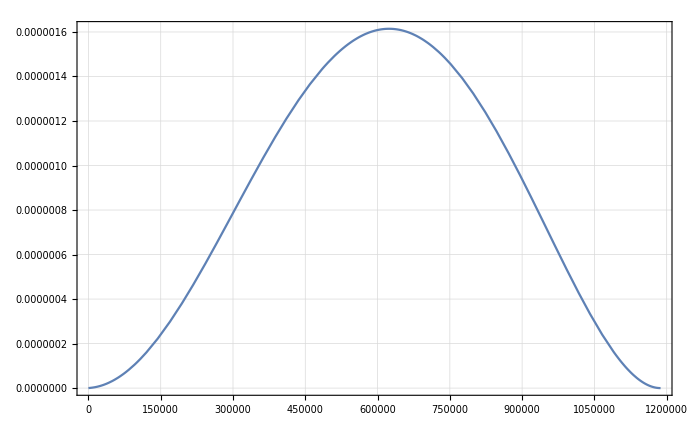

```mathematica
Plot[wmomInterNormedWb[0.,p],{p,0,pmax}]
```

```mathematica
Get["Bfield+Drift/Bfields.m"]
```

```mathematica
?BBarPolyWg
```

test with arguments: p_?NumericQ, th2_?NumericQ, B_?NumericQ, R_?NumericQ, 
  G1_?NumericQ, G2_?NumericQ, y0_?NumericQ

```mathematica
ClearAll[testint]
```

```mathematica
testint[f_[x___],intVarAndLimits__]:=NIntegrate[f[x],intVarAndLimits]
```

```mathematica
testf[x_?NumericQ]:=x^2
```

```mathematica
testf[w]
```

testf[w]

```mathematica
testint[testf[x],{x,0,1},{y,0,1}]
```

0.333333

```mathematica
FullForm[testint[Plus[x,y,z]]]
```

Plus[1,x,y,z]